## Capítulo 3: Conjuntos de Julia

```mathematica
h = #^2 -1
```

```mathematica
NestList[
```

## 3.1. La familia de funciones z^2+c

```mathematica
M=50;
Julia[z_,c_] := Length[FixedPointList[#^2+c &, z, M, SameTest->(Abs[#]>Max[2.0, Abs[c]] &)]];
```

```mathematica
DensityPlot[Julia[x+I y, -0.12+0.75 I], {x,-1.5,1.5},{y,-1.25,1.25}, Mesh->False,Frame->False, Axes->False, PlotPoints->200, AspectRatio->Automatic, ColorFunction->(If[# ≥ 1, RGBColor[0,0,0], Hue[#]] &) ]
```

```mathematica
DensityPlot[Julia[x+I y, -0.23+0.65 I], {x,-1.5,1.5},{y,-1.25,1.25}, Mesh->False, Axes->False, PlotPoints->200, AspectRatio->Automatic, ColorFunction->(If[# ≥ 1, RGBColor[0,0,0], Hue[#]] &) ]
```

La función JuliaSetPlot hace lo mismo pero es más sencilla de usar

```mathematica
JuliaSetPlot[-0.23+0.69I, Frame->False]
```

```mathematica
JuliaSetPlot[0.16-0.59I, Frame->False]
```

```mathematica
JuliaSetPlot[-0.5-0.6I, PlotRange->{{-0.6,-0.3},{-0.5,0}}]
```

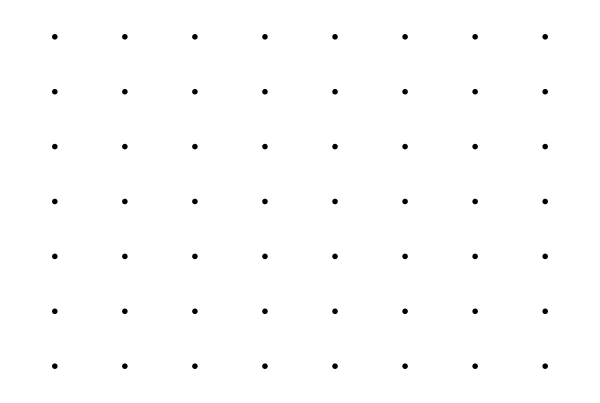

```mathematica
GraphicsGrid[Table[DensityPlot[Julia[x+I y, a+b I],{x,-1.4,1.4},{y,-1.1,1.1}, Mesh->False,Frame->False,PlotPoints->100,Axes->False,AspectRatio->Automatic],{b,-0.9,0.9,0.1},{a,-1.5,0.6,0.1}],ImageSize->600]
```

```mathematica
conjuntoJulia[z_,c_] := Mod[Length[FixedPointList[#^2+c &, z, 50, SameTest->(Abs[#]>2.0 &)]],50];
```

```mathematica
DensityPlot[conjuntoJulia[x+y I, -0.5-0.6I], {x,-2,2}, {y,-1.1,1.1}, Mesh->False, Frame->False, PlotPoints->200, Axes->False, AspectRatio->Automatic]
```

```mathematica
DensityPlot[Julia[x+I y, -0.23+0.65 I], {x,-.2,1.5},{y,-1.2,.5}, Mesh->False, Axes->False, PlotPoints->200, AspectRatio->Automatic, ColorFunction->(If[# ≥ 1, RGBColor[0,0,0], Hue[#]] &) ]
```

```mathematica
DensityPlot[Julia[x+I y, -0.23+0.65 I], {x,.6,1.4},{y,-0.9,-.1}, Mesh->False, Axes->False, PlotPoints->200, AspectRatio->Automatic, ColorFunction->(If[# ≥ 1, RGBColor[0,0,0], Hue[#]] &) ]
```

```mathematica
DensityPlot[Julia[x+I y, -0.23+0.65 I], {x,1.05,1.35},{y,-0.63,-.35}, Mesh->False, Axes->False, PlotPoints->200, AspectRatio->Automatic, ColorFunction->(If[# ≥ 1, RGBColor[0,0,0], Hue[#]] &) ]
```

## 3.2. Mathematica y conjuntos de Julia para funciones no polinómicas

### 3.2.1. La familia c*Sin(z)

```mathematica
JuliaS = Compile[{{z,_Complex},{c,_Complex}, {Max, _Integer}}, Length[FixedPointList[c Sin[#] &,z,Max, SameTest->(Re[#2]>20. &)]]];
```

```mathematica
DensityPlot[JuliaS[x+y I, 1+0.3 I, 50], {x,-0.1, 12.5}, {y, -5.2,5.2}, PlotPoints->250, AspectRatio->Automatic, ColorFunction->(If[#≥1, Hue[0,0,0],Hue[#]]&)]
```

```mathematica
conjuntoJuliaSin = Compile[{{z, _Complex},{c,_Complex}, {Max, _Integer}}, Length[FixedPointList[c*Sin[#] &, z,Max,SameTest->(Re[#2]>50. &)]]];
```

```mathematica
DensityPlot[conjuntoJuliaSin[x+y I,1+0.3I,50], {x,-1,1}, {y,-1,1}, Mesh->False, Frame->False, PlotPoints->250, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, Hue[0,0,0], Hue[#]] &)]
```

```mathematica
DensityPlot[conjuntoJuliaSin[x+y I,-2,50], {x,-5,5}, {y,-5,5}, Mesh->False, Frame->False, PlotPoints->250, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, Hue[0,0,0], Hue[#]] &)]
```

### 3.2.2. La familia c*Cos(z)

```mathematica
conjuntoJuliaCos = Compile[{{z, _Complex},{c,_Complex}, {Max, _Integer}}, Length[FixedPointList[c*Cos[#] &, z,Max,SameTest->(Re[#2]>50. &)]]];
```

```mathematica
DensityPlot[conjuntoJuliaCos[x+y I,4,50], {x,-5,5}, {y,-5,5}, Mesh->False, Frame->False, PlotPoints->100, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, RGBColor[1,1,1], Hue[1-2#]] &)]
```

```mathematica
DensityPlot[conjuntoJuliaCos[x+y I,4,50], {x,-1,1}, {y,-1,1}, Mesh->False, Frame->False, PlotPoints->100, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, RGBColor[1,1,1], Hue[1-2#]] &)]
```

### 3.2.3. La familia c*e^z

```mathematica
conjuntoJuliaExp = Compile[{{z, _Complex},{c,_Complex}, {Max, _Integer}}, Length[FixedPointList[c*E^# &, z,Max,SameTest->(Re[#2]>50. &)]]];
```

```mathematica
DensityPlot[conjuntoJuliaExp[x+y I,1+2I,50], {x,-2,4}, {y,2,7}, Mesh->False, Frame->False, PlotPoints->100, Axes->False, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, RGBColor[1,1,1], Hue[1-2#]] &)]
```

```mathematica
DensityPlot[conjuntoJuliaExp[x+y I,3I,50], {x,-6,5}, {y,-5,5}, Mesh->False, Frame->False, PlotPoints->100, AspectRatio->Automatic, ColorFunction->(If[#≥ 1, RGBColor[1,1,1], Hue[1-2#]] &)]
```